Fixpunkte des Micropillar Lasersystems mit Feedback (Ν ist hier ein griechisches Nu):

```mathematica
Solve[{0==(Ν S)/(1+T)-S/τs,0==(J0+κ S-Ν)/τn-(Ν S)/(1+T),0==(cs S-T)/τt},{S,Ν,T}]
```

{{S→0,Ν→J0,T→0},{S→(-1+J0 τs)/(cs+τn-κ τs),Ν→(τn+cs J0 τs-κ τs)/(τs (cs+τn-κ τs)),T→(-cs+cs J0 τs)/(cs+τn-κ τs)}}

Jacobi-Matrix:

```mathematica
M=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J0+κ S-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{S,Ν,T}}]];
MatrixForm[M]
```

(Ν/(1+T)-1/τs | S/(1+T) | -(S Ν)/(1+T)^2
-Ν/(1+T)+κ/τn | -(1+T+S τn)/(τn+T τn) | (S Ν)/(1+T)^2
cs/τt | 0 | -1/τt)

Fixpunkt x_1^* in Jacobi-Matrix einsetzen:

```mathematica
S=0;Ν=J0;T=0;
MatrixForm[M]
```

(J0-1/τs | 0 | 0
-J0+κ/τn | -1/τn | 0
cs/τt | 0 | -1/τt)

Variablen S, Ν und T wieder freigeben, um zweiten Fixpunkt x_2^* einsetzen zu können:

```mathematica
S=.;Ν=.;T=.;
```

Fixpunkt x_2^* in Jacobi-Matrix einsetzen:

```mathematica
S=(τs J0-1)/(cs+τn-κ τs);Ν=(τn+τs(cs J0-κ))/(τs (cs+τn-κ τs));T=(cs (τs J0 -1))/(cs+τn-κ τs);
FullSimplify[MatrixForm[M]]
```

(0 | (-1+J0 τs)/(τn+cs J0 τs-κ τs) | (1-J0 τs)/(τs (τn+cs J0 τs-κ τs))
κ/τn-1/τs | ((κ-J0 (cs+τn)) τs)/(τn (τn+cs J0 τs-κ τs)) | (-1+J0 τs)/(τs (τn+cs J0 τs-κ τs))
cs/τt | 0 | -1/τt)

Bestimmung der Eigenwerte mit dem Parameterset des Reizenstein-Experiments, da Mathematica die Eigenwerte für die allgemeine Analyse nicht berechnen kann:

```mathematica
S=.;Ν=.;T=.;τs=.;τn=.;τt=.;β=.;κ=.;cs=.;J0=.;
M=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J0+κ S-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{S,Ν,T}}]];
S=(τs J0-1)/(cs+τn-κ τs);Ν=(τn+τs(cs J0-κ))/(τs (cs+τn-κ τs));T=(cs (τs J0 -1))/(cs+τn-κ τs);
FullSimplify[M];
τs=10^-2;
τn=10^-2;
τt=6*10^3;
κ=1.000042;(*Stabilitätsgrenze bei 1.000042;*)
cs=0.08;
J0=150;
EV=Eigenvalues[M];
λ1=Part[EV,1]
λ2=Part[EV,2]
λ3=Part[EV,3]
```

-104.167

-3.99899×10^-7+0.0730295 ⅈ

-3.99899×10^-7-0.0730295 ⅈ

Setzen der Parameter für das Bifurkationsdiagramm λ(J_0):

```mathematica
S=.;Ν=.;T=.;τs=.;τn=.;τt=.;β=.;κ=.;cs=.;J0=.;
M=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J0+κ S-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{S,Ν,T}}]];
S=(τs J0-1)/(cs+τn-κ τs);Ν=(τn+τs(cs J0-κ))/(τs (cs+τn-κ τs));T=(cs (τs J0 -1))/(cs+τn-κ τs);
τs=10^-2;
τn=10^-2;
τt=6*10^3;
cs=0.08;
EV=Eigenvalues[M];
λ1=Part[EV,1];
λ2=Part[EV,2];
λ3=Part[EV,3];
```

Eigenwerte in Abhängigkeit von J_0 für verschiedene κ:

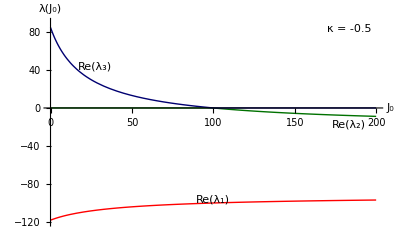

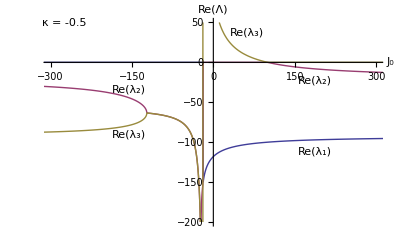

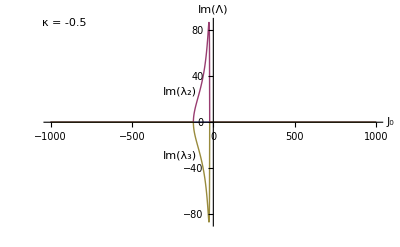

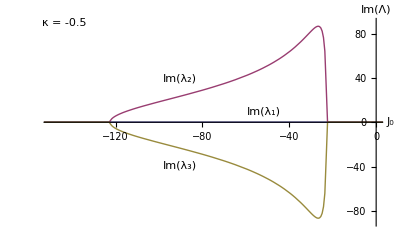

```mathematica
κ=-0.5;
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J0,0,200},AxesLabel->{"J_0","λ(J_0)"},AxesOrigin->{0,0},PlotRange->{{0,200},{-120,90}},PlotStyle->{Red,Darker[Darker[Green]],Darker[Darker[Blue]]},Epilog->{Text["κ = -0.5",Scaled[{.90,.95}]],Text["Re(λ_1)",Scaled[{.50,.13}]],Text["Re(λ_2)",Scaled[{.90,.49}]],Text["Re(λ_3)",Scaled[{.15,.77}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{-300,300},{-200,50}},Epilog->{Text["κ = -0.5",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.80,.36}]],Text["Re(λ_2)",Scaled[{.25,.66}]],Text["Re(λ_2)",Scaled[{.80,.70}]],Text["Re(λ_3)",Scaled[{.25,.44}]],Text["Re(λ_3)",Scaled[{.60,.93}]]}]

Plot[{Im[λ1],Im[λ2],Im[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Im(Λ)"},AxesOrigin->{0,0},Epilog->{Text["κ = -0.5",Scaled[{.06,.98}]],Text["Im(λ_2)",Scaled[{.40,.65}]],Text["Im(λ_3)",Scaled[{.40,.34}]]}]
Plot[{Im[λ1],Im[λ2],Im[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Im(Λ)"},AxesOrigin->{0,0},PlotRange->{{-150,0},{-90,90}},Epilog->{Text["κ = -0.5",Scaled[{.06,.98}]],Text["Im(λ_1)",Scaled[{.65,.55}]],Text["Im(λ_2)",Scaled[{.40,.71}]],Text["Im(λ_3)",Scaled[{.40,.29}]]}]
```

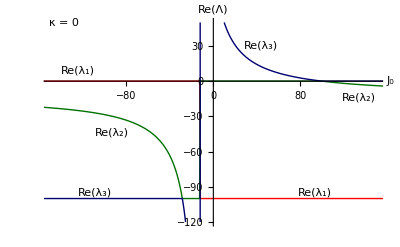

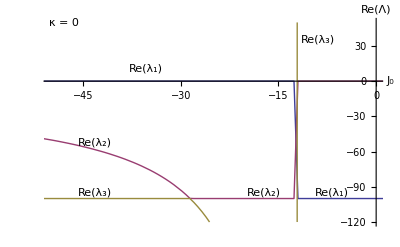

```mathematica
κ=0;
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{-150,150},{-120,50}},PlotStyle->{Red,Darker[Darker[Green]],Darker[Darker[Blue]]},Epilog->{Text["κ = 0",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.10,.75}]],Text["Re(λ_1)",Scaled[{.80,.16}]],Text["Re(λ_2)",Scaled[{.20,.45}]],Text["Re(λ_2)",Scaled[{.93,.62}]],Text["Re(λ_3)",Scaled[{.15,.16}]],Text["Re(λ_3)",Scaled[{.64,.87}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{-50,0},{-120,50}},Epilog->{Text["κ = 0",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.30,.76}]],Text["Re(λ_1)",Scaled[{.85,.16}]],Text["Re(λ_2)",Scaled[{.15,.40}]],Text["Re(λ_2)",Scaled[{.65,.16}]],Text["Re(λ_3)",Scaled[{.15,.16}]],Text["Re(λ_3)",Scaled[{.81,.90}]]}]
```

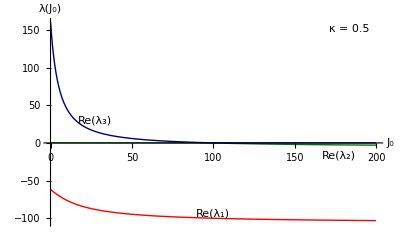

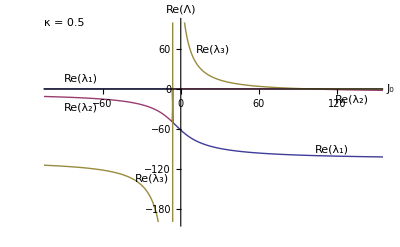

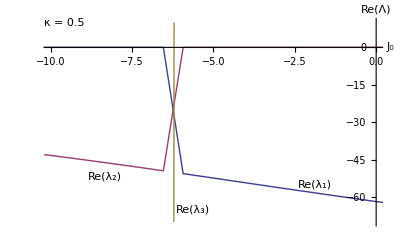

```mathematica
κ=0.5;
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J0,0,200},AxesLabel->{"J_0","λ(J_0)"},AxesOrigin->{0,0},PlotRange->{{0,200},{-105,160}},PlotStyle->{Red,Darker[Darker[Green]],Darker[Darker[Blue]]},Epilog->{Text["κ = 0.5",Scaled[{.90,.95}]],Text["Re(λ_1)",Scaled[{.50,.06}]],Text["Re(λ_2)",Scaled[{.87,.34}]],Text["Re(λ_3)",Scaled[{.15,.51}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{-100,150},{-200,100}},Epilog->{Text["κ = 0.5",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.11,.71}]],Text["Re(λ_1)",Scaled[{.85,.37}]],Text["Re(λ_2)",Scaled[{.11,.57}]],Text["Re(λ_2)",Scaled[{.91,.61}]],Text["Re(λ_3)",Scaled[{.32,.23}]],Text["Re(λ_3)",Scaled[{.50,.85}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{-10,0},{-70,10}},Epilog->{Text["κ = 0.5",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.80,.20}]],Text["Re(λ_2)",Scaled[{.18,.24}]],Text["Re(λ_3)",Scaled[{.44,.08}]]}]
```

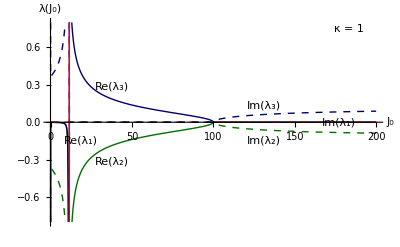

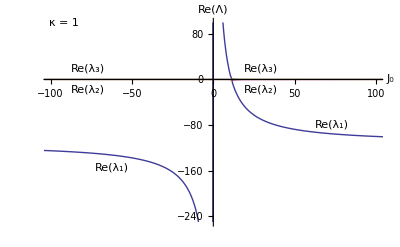

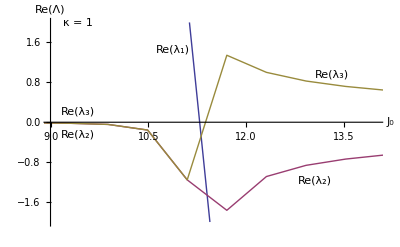

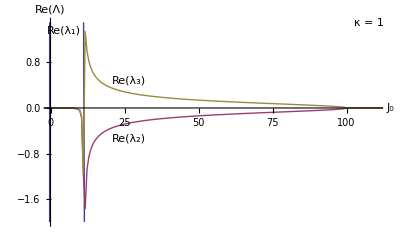

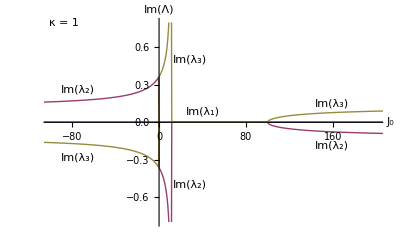

```mathematica
κ=1;
Plot[{Re[λ2],Re[λ3],Im[λ1],Im[λ2],Im[λ3],Re[λ1]},{J0,0,200},AxesLabel->{"J_0","λ(J_0)"},AxesOrigin->{0,0},PlotRange->{{0,200},{-0.8,0.8}},PlotStyle->{Darker[Darker[Green]],Darker[Darker[Blue]],{Red,Dashed},{Darker[Darker[Green]],Dashed},{Darker[Darker[Blue]],Dashed},Red},Epilog->{Text["κ = 1",Scaled[{.90,.95}]],Text["Re(λ_1)",Scaled[{.11,.41}]],Text["Re(λ_2)",Scaled[{.20,.31}]],Text["Re(λ_3)",Scaled[{.20,.67}]],Text["Im(λ_1)",Scaled[{.87,.50}]],Text["Im(λ_2)",Scaled[{.65,.41}]],,Text["Im(λ_3)",Scaled[{.65,.58}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{-100,100},{-250,100}},Epilog->{Text["κ = 1",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.20,.28}]],Text["Re(λ_1)",Scaled[{.85,.49}]],Text["Re(λ_2)",Scaled[{.13,.66}]],Text["Re(λ_2)",Scaled[{.64,.66}]],Text["Re(λ_3)",Scaled[{.13,.76}]],Text["Re(λ_3)",Scaled[{.64,.76}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Re(Λ)"},AxesOrigin->{9,0},PlotRange->{{9,14},{-2,2}},Epilog->{Text["κ = 1",Scaled[{.10,.98}]],Text["Re(λ_1)",Scaled[{.38,.85}]],Text["Re(λ_2)",Scaled[{.10,.44}]],Text["Re(λ_2)",Scaled[{.80,.22}]],Text["Re(λ_3)",Scaled[{.10,.55}]],Text["Re(λ_3)",Scaled[{.85,.73}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{0,110},{-2,1.5}},Epilog->{Text["κ = 1",Scaled[{.96,.98}]],Text["Re(λ_1)",Scaled[{.06,.94}]],Text["Re(λ_2)",Scaled[{.25,.42}]],Text["Re(λ_3)",Scaled[{.25,.70}]]}]

Plot[{Im[λ1],Im[λ2],Im[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Im(Λ)"},AxesOrigin->{0,0},PlotRange->{{-100,200},{-0.8,0.8}},Epilog->{Text["κ = 1",Scaled[{.06,.98}]],Text["Im(λ_1)",Scaled[{.47,.55}]],Text["Im(λ_2)",Scaled[{.10,.66}]],Text["Im(λ_2)",Scaled[{.43,.20}]],Text["Im(λ_2)",Scaled[{.85,.39}]],Text["Im(λ_3)",Scaled[{.10,.33}]],Text["Im(λ_3)",Scaled[{.43,.80}]],Text["Im(λ_3)",Scaled[{.85,.59}]]}]
```

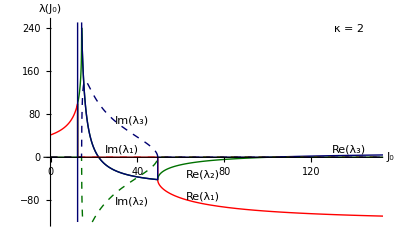

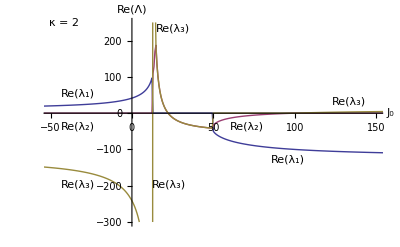

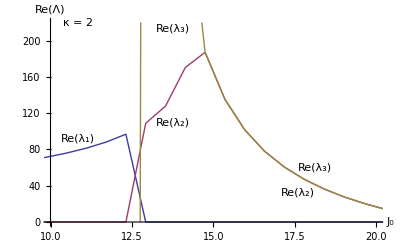

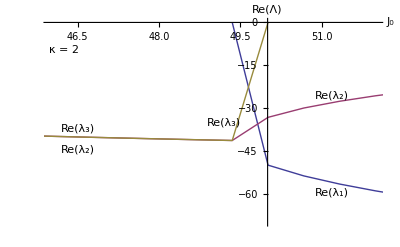

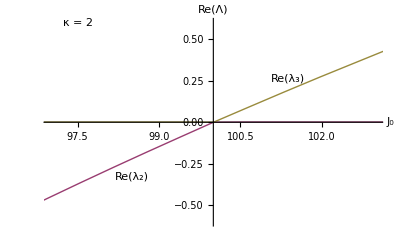

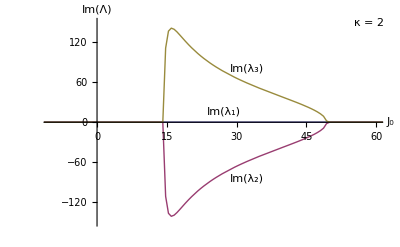

```mathematica
κ=2;
Plot[{Re[λ1],Re[λ2],Re[λ3],Im[λ1],Im[λ2],Im[λ3]},{J0,0,200},AxesLabel->{"J_0","λ(J_0)"},PlotRange->{{0,150},{-120,250}},PlotStyle->{Red,Darker[Darker[Green]],Darker[Darker[Blue]],{Red,Dashed},{Darker[Darker[Green]],Dashed},{Darker[Darker[Blue]],Dashed}},Epilog->{Text["κ = 2",Scaled[{.90,.95}]],Text["Re(λ_1)",Scaled[{.47,.14}]],Text["Re(λ_2)",Scaled[{.47,.25}]],Text["Re(λ_3)",Scaled[{.90,.37}]],Text["Im(λ_1)",Scaled[{.23,.37}]],Text["Im(λ_2)",Scaled[{.26,.12}]],Text["Im(λ_3)",Scaled[{.26,.51}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{-50,150},{-300,250}},Epilog->{Text["κ = 2",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.10,.64}]],Text["Re(λ_1)",Scaled[{.72,.32}]],Text["Re(λ_2)",Scaled[{.10,.48}]],Text["Re(λ_2)",Scaled[{.60,.48}]],Text["Re(λ_3)",Scaled[{.10,.20}]],Text["Re(λ_3)",Scaled[{.37,.20}]],Text["Re(λ_3)",Scaled[{.38,.95}]],Text["Re(λ_3)",Scaled[{.90,.60}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Re(Λ)"},AxesOrigin->{10,0},PlotRange->{{10,20},{0,220}},Epilog->{Text["κ = 2",Scaled[{.10,.98}]],Text["Re(λ_1)",Scaled[{.10,.42}]],Text["Re(λ_2)",Scaled[{.38,.50}]],Text["Re(λ_2)",Scaled[{.75,.16}]],Text["Re(λ_3)",Scaled[{.38,.95}]],Text["Re(λ_3)",Scaled[{.80,.28}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Re(Λ)"},AxesOrigin->{50,0},PlotRange->{{46,52},{-70,0}},Epilog->{Text["κ = 2",Scaled[{.06,.85}]],Text["Re(λ_1)",Scaled[{.85,.16}]],Text["Re(λ_2)",Scaled[{.10,.37}]],Text["Re(λ_2)",Scaled[{.85,.63}]],Text["Re(λ_3)",Scaled[{.10,.47}]],Text["Re(λ_3)",Scaled[{.53,.50}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Re(Λ)"},AxesOrigin->{100,0},PlotRange->{{97,103},{-0.6,0.6}},Epilog->{Text["κ = 2",Scaled[{.10,.98}]],Text["Re(λ_2)",Scaled[{.26,.24}]],Text["Re(λ_3)",Scaled[{.72,.71}]]}]

Plot[{Im[λ1],Im[λ2],Im[λ3]},{J0,-1000,1000},AxesLabel->{"J_0","Im(Λ)"},AxesOrigin->{0,0},PlotRange->{{-10,60},{-150,150}},Epilog->{Text["κ = 2",Scaled[{.96,.98}]],Text["Im(λ_1)",Scaled[{.53,.55}]],Text["Im(λ_2)",Scaled[{.60,.23}]],Text["Im(λ_3)",Scaled[{.60,.76}]]}]
```

Setzen der Parameter für das Bifurkationsdiagramm λ(S):

```mathematica
S=.;Ν=.;T=.;τs=.;τn=.;τt=.;β=.;κ=.;cs=.;J0=.;
M=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J0+κ S-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{S,Ν,T}}]];
S=(τs J0-1)/(cs+τn-κ τs);Ν=(τn+τs(cs J0-κ))/(τs (cs+τn-κ τs));T=(cs (τs J0 -1))/(cs+τn-κ τs);
τs=10^-2;
τn=10^-2;
τt=6*10^3;
cs=0.08;
S=.;
J0=(S(cs+τn-κ τs)+1)/τs;
EV=Eigenvalues[M];
λ1=Part[EV,1];
λ2=Part[EV,2];
λ3=Part[EV,3];
```

Eigenwerte in Abhängigkeit von S für verschiedene κ:

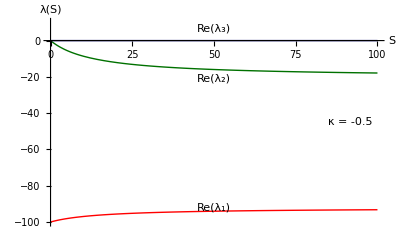

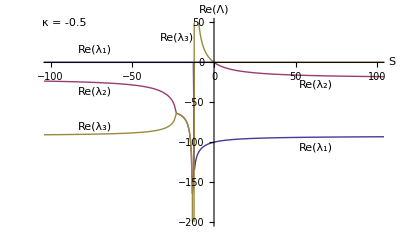

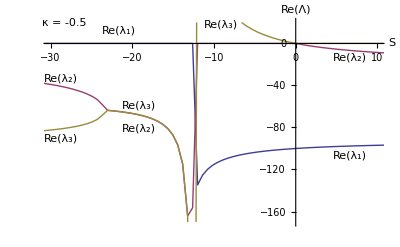

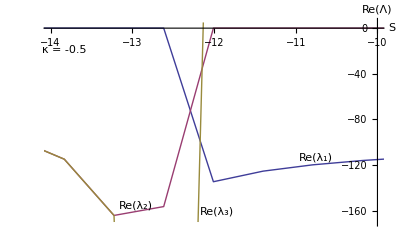

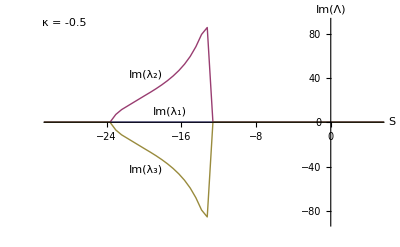

```mathematica
κ=-0.5;
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,0,100},AxesLabel->{"S","λ(S)"},PlotRange->{{0,100},{-100,10}},PlotStyle->{Red,Darker[Darker[Green]],Darker[Darker[Blue]]},Epilog->{Text["κ = -0.5",Scaled[{.90,.50}]],Text["Re(λ_1)",Scaled[{.50,.09}]],Text["Re(λ_2)",Scaled[{.50,.71}]],Text["Re(λ_3)",Scaled[{.50,.95}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,-1000,1000},AxesLabel->{"S","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{-100,100},{-200,50}},Epilog->{Text["κ = -0.5",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.15,.85}]],Text["Re(λ_1)",Scaled[{.80,.38}]],Text["Re(λ_2)",Scaled[{.15,.65}]],Text["Re(λ_2)",Scaled[{.80,.68}]],Text["Re(λ_3)",Scaled[{.15,.48}]],Text["Re(λ_3)",Scaled[{.39,.91}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,-1000,1000},AxesLabel->{"S","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{-30,10},{-170,20}},Epilog->{Text["κ = -0.5",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.22,.94}]],Text["Re(λ_1)",Scaled[{.90,.34}]],Text["Re(λ_2)",Scaled[{.05,.71}]],Text["Re(λ_2)",Scaled[{.28,.47}]],Text["Re(λ_2)",Scaled[{.90,.81}]],Text["Re(λ_3)",Scaled[{.05,.42}]],Text["Re(λ_3)",Scaled[{.28,.58}]],Text["Re(λ_3)",Scaled[{.52,.97}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,-1000,1000},AxesLabel->{"S","Re(Λ)"},AxesOrigin->{-10,0},PlotRange->{{-14,-10},{-170,5}},Epilog->{Text["κ = -0.5",Scaled[{.06,.85}]],Text["Re(λ_1)",Scaled[{.80,.33}]],Text["Re(λ_2)",Scaled[{.27,.10}]],Text["Re(λ_3)",Scaled[{.51,.07}]]}]

Plot[{Im[λ1],Im[λ2],Im[λ3]},{S,-1000,1000},AxesLabel->{"S","Im(Λ)"},AxesOrigin->{0,0},PlotRange->{{-30,5},{-90,90}},Epilog->{Text["κ = -0.5",Scaled[{.06,.98}]],Text["Im(λ_1)",Scaled[{.37,.55}]],Text["Im(λ_2)",Scaled[{.30,.73}]],Text["Im(λ_3)",Scaled[{.30,.27}]]}]
```

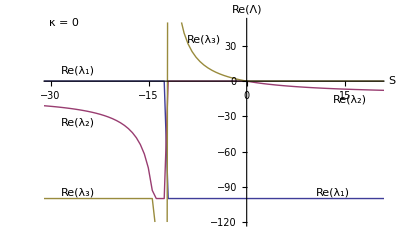

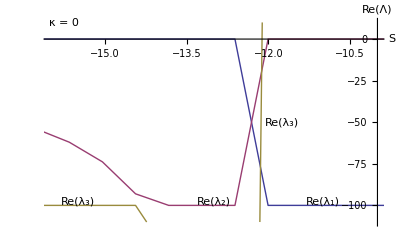

```mathematica
κ=0;
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,-1000,1000},AxesLabel->{"S","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{-30,20},{-120,50}},Epilog->{Text["κ = 0",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.10,.75}]],,Text["Re(λ_1)",Scaled[{.85,.16}]],Text["Re(λ_2)",Scaled[{.10,.50}]],Text["Re(λ_2)",Scaled[{.90,.61}]],Text["Re(λ_3)",Scaled[{.10,.16}]],Text["Re(λ_3)",Scaled[{.47,.90}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,-1000,1000},AxesLabel->{"S","Re(Λ)"},AxesOrigin->{-10,0},PlotRange->{{-16,-10},{-110,10}},Epilog->{Text["κ = 0",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.82,.12}]],Text["Re(λ_2)",Scaled[{.50,.12}]],Text["Re(λ_3)",Scaled[{.10,.12}]],Text["Re(λ_3)",Scaled[{.70,.50}]]}]
```

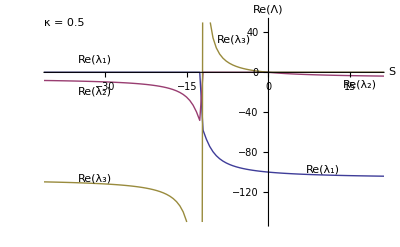

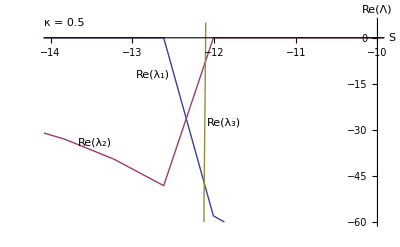

```mathematica
κ=0.5;
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,-1000,1000},AxesLabel->{"S","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{-40,20},{-150,50}},Epilog->{Text["κ = 0.5",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.15,.80}]],Text["Re(λ_1)",Scaled[{.82,.27}]],Text["Re(λ_2)",Scaled[{.15,.65}]],Text["Re(λ_2)",Scaled[{.93,.68}]],Text["Re(λ_3)",Scaled[{.15,.23}]],Text["Re(λ_3)",Scaled[{.56,.90}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,-1000,1000},AxesLabel->{"S","Re(Λ)"},AxesOrigin->{-10,0},PlotRange->{{-14,-10},{-60,5}},Epilog->{Text["κ = 0.5",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.32,.73}]],Text["Re(λ_2)",Scaled[{.15,.40}]],Text["Re(λ_3)",Scaled[{.53,.50}]]}]
```

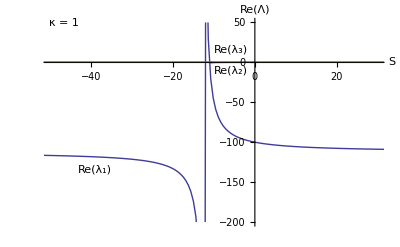

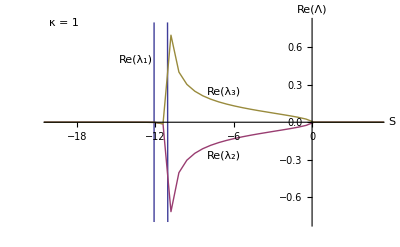

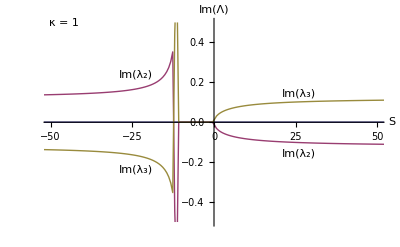

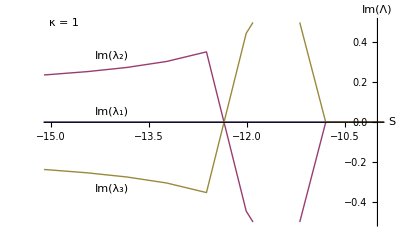

```mathematica
κ=1;
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,-1000,1000},AxesLabel->{"S","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{-50,30},{-200,50}},Epilog->{Text["κ = 1",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.15,.27}]],Text["Re(λ_2)",Scaled[{.55,.75}]],Text["Re(λ_3)",Scaled[{.55,.85}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,-1000,1000},AxesLabel->{"S","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{-20,5},{-0.8,0.8}},Epilog->{Text["κ = 1",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.27,.80}]],Text["Re(λ_2)",Scaled[{.53,.34}]],Text["Re(λ_3)",Scaled[{.53,.65}]]}]

Plot[{Im[λ1],Im[λ2],Im[λ3]},{S,-1000,1000},AxesLabel->{"S","Im(Λ)"},AxesOrigin->{0,0},PlotRange->{{-50,50},{-0.5,0.5}},Epilog->{Text["κ = 1",Scaled[{.06,.98}]],Text["Im(λ_2)",Scaled[{.27,.73}]],Text["Im(λ_2)",Scaled[{.75,.35}]],Text["Im(λ_3)",Scaled[{.27,.27}]],Text["Im(λ_3)",Scaled[{.75,.64}]]}]
Plot[{Im[λ1],Im[λ2],Im[λ3]},{S,-1000,1000},AxesLabel->{"S","Im(Λ)"},AxesOrigin->{-10,0},PlotRange->{{-15,-10},{-0.5,0.5}},Epilog->{Text["κ = 1",Scaled[{.06,.98}]],Text["Im(λ_1)",Scaled[{.20,.55}]],Text["Im(λ_2)",Scaled[{.20,.82}]],Text["Im(λ_3)",Scaled[{.20,.18}]]}]
```

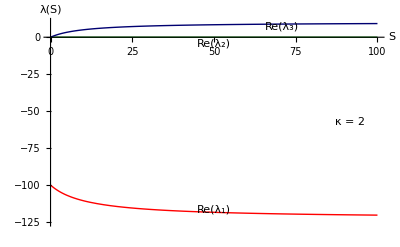

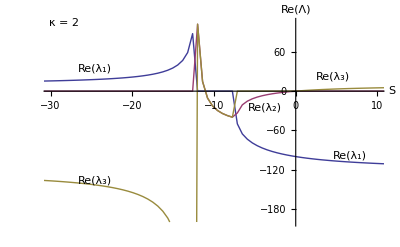

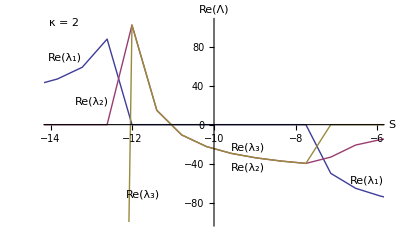

```mathematica
κ=2;
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,0,100},AxesLabel->{"S","λ(S)"},PlotRange->{{0,100},{-125,10}},PlotStyle->{Red,Darker[Darker[Green]],Darker[Darker[Blue]]},Epilog->{Text["κ = 2",Scaled[{.90,.50}]],Text["Re(λ_1)",Scaled[{.50,.08}]],Text["Re(λ_2)",Scaled[{.50,.88}]],Text["Re(λ_3)",Scaled[{.70,.96}]]}]

Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,-1000,1000},AxesLabel->{"S","Re(Λ)"},AxesOrigin->{0,0},PlotRange->{{-30,10},{-200,105}},Epilog->{Text["κ = 2",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.15,.76}]],Text["Re(λ_1)",Scaled[{.90,.34}]],Text["Re(λ_2)",Scaled[{.65,.57}]],Text["Re(λ_3)",Scaled[{.15,.22}]],Text["Re(λ_3)",Scaled[{.85,.72}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,-1000,1000},AxesLabel->{"S","Re(Λ)"},AxesOrigin->{-10,0},PlotRange->{{-14,-6},{-100,105}},Epilog->{Text["κ = 2",Scaled[{.06,.98}]],Text["Re(λ_1)",Scaled[{.06,.81}]],Text["Re(λ_1)",Scaled[{.95,.22}]],Text["Re(λ_2)",Scaled[{.14,.60}]],Text["Re(λ_2)",Scaled[{.60,.28}]],Text["Re(λ_3)",Scaled[{.29,.15}]],Text["Re(λ_3)",Scaled[{.60,.38}]]}]
```

Stabilitätsanalyse bezüglich κ:

```mathematica
S=.;Ν=.;T=.;τs=.;τn=.;τt=.;cs=.;J0=.;
τs=10^-2;
τn=10^-2;
τt=6*10^3;
cs=0.08;
J0=150;
M=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J0+κ S-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{S,Ν,T}}]];
S=(τs J0-1)/(cs+τn-κ τs);Ν=(τn+τs(cs J0-κ))/(τs (cs+τn-κ τs));T=(cs (τs J0 -1))/(cs+τn-κ τs);
FullSimplify[M];

κreλ1=κimλ1=κreλ2=κimλ2=κreλ3=κimλ3=Range[0];
step=0.001;
min=0;
max=9-step;
ProgressIndicator[Dynamic[κ],{min,max}]

Do[EV=Eigenvalues[M];
λ1=Part[EV,1];
λ2=Part[EV,2];
λ3=Part[EV,3];
κreλ1=Append[κreλ1,{κ,Re[λ1]}];
κimλ1=Append[κimλ1,{κ,Im[λ1]}];
κreλ2=Append[κreλ2,{κ,Re[λ2]}];
κimλ2=Append[κimλ2,{κ,Im[λ2]}];
κreλ3=Append[κreλ3,{κ,Re[λ3]}];
κimλ3=Append[κimλ3,{κ,Im[λ3]}],
{κ,min,max,step}]
```

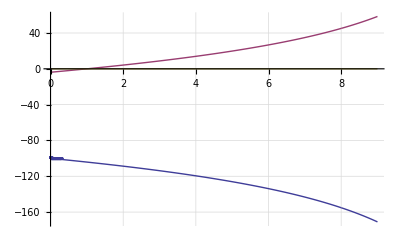

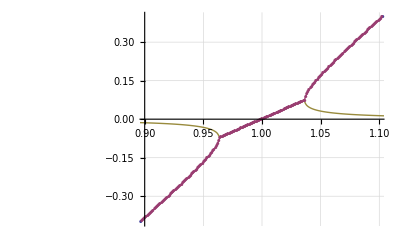

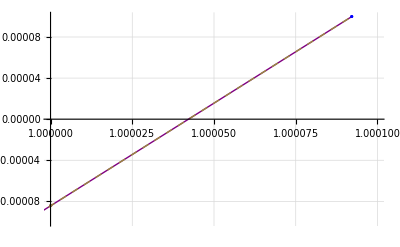

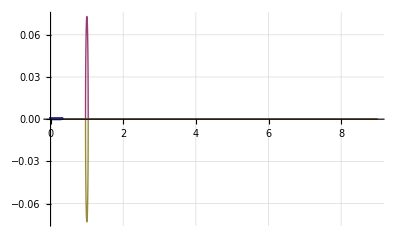

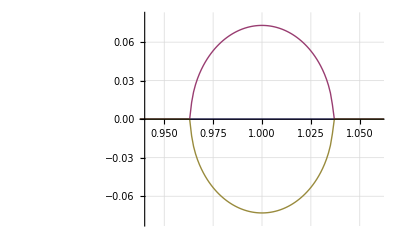

```mathematica
ListLinePlot[{κreλ1,κreλ2,κreλ3},AxesLabel->{"κ","Re(λ(κ))"},PlotRange->All,PlotMarkers->{●,2},GridLines->Automatic,Epilog->{Text["Re(λ_1)",Scaled[{.55,.26}]],Text["Re(λ_2)",Scaled[{.55,.87}]],Text["Re(λ_3)",Scaled[{.77,.67}]]}]
ListLinePlot[{κreλ1,κreλ2,κreλ3},AxesLabel->{"κ","Re(λ(κ))"},PlotRange->{{0.9,1.1},{-0.4,0.4}},PlotMarkers->{●,2},GridLines->Automatic,Epilog->{Text["Re(λ_2)",Scaled[{.09,.20}]],Text["Re(λ_3)",Scaled[{.86,.57}]]}]
ListLinePlot[{κreλ1,κreλ2,κreλ3},AxesLabel->{"κ","Re(λ(κ))"},PlotRange->{{1,1.0001},{-0.0001,0.0001}},PlotMarkers->{●,2},PlotStyle->{Blue,Purple,Dashed},GridLines->Automatic,Epilog->{Text["Re(λ_2)",Scaled[{.57,.55}]],Text["Re(λ_3)",Scaled[{.50,.65}]]}]

ListLinePlot[{κimλ1,κimλ2,κimλ3},AxesLabel->{"κ","Im(λ(κ))"},PlotRange->All,PlotMarkers->{●,2},GridLines->Automatic,Epilog->{Text["Im(λ_2)",Scaled[{.19,.80}]],Text["Im(λ_3)",Scaled[{.19,.16}]]}]
ListLinePlot[{κimλ1,κimλ2,κimλ3},AxesLabel->{"κ","Im(λ(κ))"},PlotRange->{{0.94,1.06},{-0.08,0.08}},PlotMarkers->{●,2},GridLines->Automatic,Epilog->{Text["Im(λ_1)",Scaled[{.40,.55}]],Text["Im(λ_2)",Scaled[{.40,.85}]],Text["Im(λ_3)",Scaled[{.40,.13}]]}]
```

Zeitverläufe S(t), Ν(t) und T(t), Phasenraumportrait S(Ν) mit Berücksichtigung des Terms für spontane Emission:

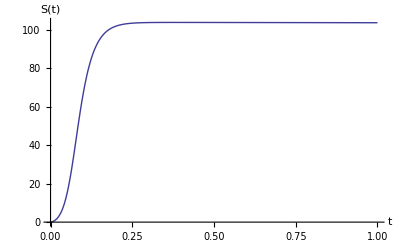

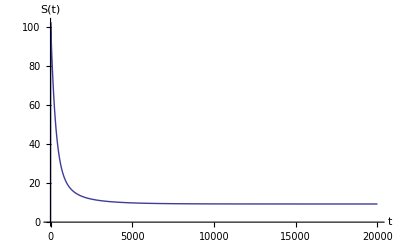

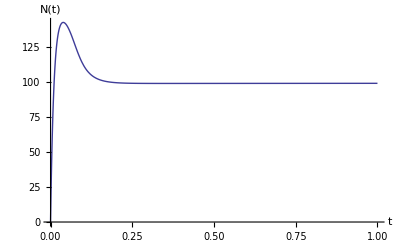

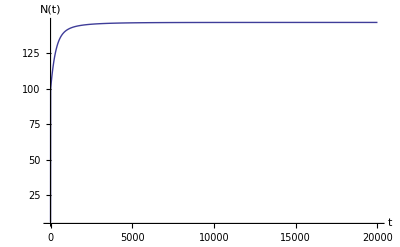

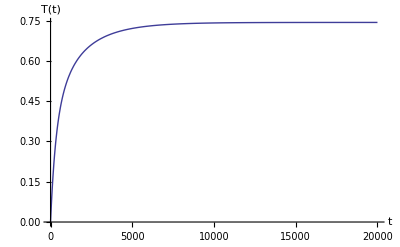

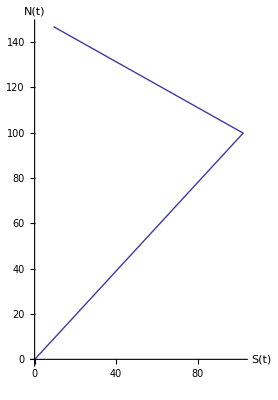

```mathematica
S=.;Ν=.;T=.;
β=0.01;
τs=10^-2;
τn=10^-2;
τt=6*10^3;
cs=0.08;
J0=150;
κ=0.5;
tmax=20000;
Sfix=(τs J0-1)/(cs+τn-κ τs);Νfix=(τn+τs(cs J0-κ))/(τs (cs+τn-κ τs));Tfix=(cs (τs J0 -1))/(cs+τn-κ τs);
Sdev=-0.99 Sfix;
Νdev=-Νfix;
Tdev=-Tfix;
s=NDSolve[{S'[t]==(Ν[t] S[t])/(1+T[t])-S[t]/τs+(β Ν[t])/τn,Ν'[t]==(J0+κ S[t]-Ν[t])/τn-(Ν[t] S[t])/(1+T[t]),T'[t]==(cs S[t]-T[t])/τt,S[0]==Sfix+Sdev,Ν[0]==Νfix+Νdev,T[0]==Tfix+Tdev},{S,Ν,T},{t,0,tmax}];
Plot[Evaluate[S[t]/.s],{t,0,tmax/20000},AxesLabel->{"t","S(t)"},PlotRange->All]
Plot[Evaluate[S[t]/.s],{t,0,tmax},AxesLabel->{"t","S(t)"},PlotRange->All]
Plot[Evaluate[Ν[t]/.s],{t,0,tmax/20000},AxesLabel->{"t","N(t)"},PlotRange->All]
Plot[Evaluate[Ν[t]/.s],{t,0,tmax},AxesLabel->{"t","N(t)"},PlotRange->All]
Plot[Evaluate[T[t]/.s],{t,0,tmax},AxesLabel->{"t","T(t)"},PlotRange->All]
ParametricPlot[Evaluate[{S[t],Ν[t]}/.s],{t,0,tmax},AxesLabel->{"S(t)","Ν(t)"},PlotRange->All]
```

Input-Output Kurve:

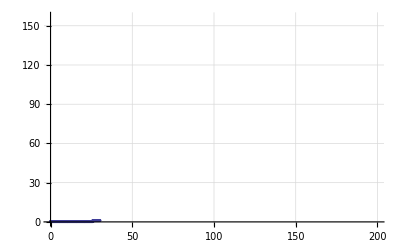

```mathematica
S=.;Ν=.;T=.;
β=0.01;
τs=10^-2;
τn=10^-2;
τt=6*10^3;
cs=0.08;
κ=0.5;
tmax=100;
Jmax=200;
step=0.1;
Sfix=0.01;Νfix=J0;Tfix=0;
Sdev=-0.99 Sfix;
Νdev=-Νfix;
Tdev=-Tfix;
a=Range[0];

ProgressIndicator[Dynamic[J0],{0,Jmax}]
Do[s=NDSolve[{S'[t]==(Ν[t] S[t])/(1+T[t])-S[t]/τs+(β Ν[t])/τn,Ν'[t]==(J0+κ S[t]-Ν[t])/τn-(Ν[t] S[t])/(1+T[t]),T'[t]==(cs S[t]-T[t])/τt,S[0]==Sfix+Sdev,Ν[0]==Νfix+Νdev,T[0]==Tfix+Tdev},{S,Ν,T},{t,0,tmax}];a=Flatten[Append[a,{J0,Evaluate[S[tmax]/.s]}]],{J0,0,Jmax,step}];
io=Partition[a,2];
ListPlot[io,AxesLabel->{"J_0","S(J_0)"},PlotMarkers->{●,3},GridLines->Automatic]
```